```mathematica
SetOptions[EvaluationNotebook[],StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],Cell[StyleData["Graphics",All],FontFamily->"CMU Serif"]},StyleDefinitions->"PrivateStylesheetFormatting.nb"]]
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
SetDirectory[NotebookDirectory[]];
<<CustomTicks`
ww0m1 = Import["ww0m1_angular.dat","List"];
ww01 = Import["ww01_angular.dat","List"];
ww10 = Import["ww10_angular.dat","List"];
wwm10 = Import["wwm10_angular.dat","List"];
ww00 = Import["ww00_angular.dat","List"];
ww11 = Import["ww11_angular.dat","List"];
wwm1m1 = Import["wwm1m1_angular.dat","List"];
ww1m1 = Import["ww1m1_angular.dat","List"];
wwm11 = Import["wwm11_angular.dat","List"];
(*dyt import*)
dytww00 = Import["ww00_angular_dyt015_linear.dat","List"];
dytww11 = Import["wwm1m1_angular_dyt015_linear.dat","List"];
dytwwm1m1 = Import["wwm1m1_angular_dyt015_linear.dat","List"];
mdytww00 = Import["ww00_angular_dytm015_linear.dat","List"];
mdytww11 = Import["wwm1m1_angular_dytm015_linear.dat","List"];
mdytwwm1m1 = Import["wwm1m1_angular_dytm015_linear.dat","List"];
```

```mathematica
(*dyt import*)
(*dytww11 = Import["ww111_angular.dat","List"];
dytwwm1m1 = Import["wwm1m1_angular_dyt0.1_1000.dat","List"];
dytww1m1 = Import["ww1m1_angular_dyt0.1_1000.dat","List"];
dytwwm11 = Import["wwm11_angular_dyt0.1_1000.dat","List"];*)
sqrtsList=Table[350+25*i,{i,0,400}];
thetaList=Table[0+(Pi/180)*i,{i,0,181}];
```

```mathematica
ww00 [[181]]
```

9.97724×10^-7

```mathematica
<<CustomTicks.m
ticks0=LogTicks[10,-3,6,TickLabelStep->1];
ticks1=ticks0;
Do[ticks1[[i,1]]=10^(ticks0[[i,1]]),{i,1,Length[ticks0]}]
ticks1;
```

```mathematica
factor=0.3894*10^12;
lineplot=ListLogPlot[{Transpose[{Cos[thetaList],factor*ww00}],Transpose[{Cos[thetaList],factor*ww01}],Transpose[{Cos[thetaList],factor*ww10}],Transpose[{Cos[thetaList],factor*ww11}],Transpose[{Cos[thetaList],factor*ww1m1}],Transpose[{Cos[thetaList],factor*wwm11}],Transpose[{Cos[thetaList],factor*(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}], Transpose[{Cos[thetaList],factor*dytww00}],Transpose[{Cos[thetaList],factor*dytww01}],Transpose[{Cos[thetaList],factor*dytww10}],Transpose[{Cos[thetaList],factor*dytww11}],Transpose[{Cos[thetaList],factor*dytww1m1}],Transpose[{Cos[thetaList],factor*dytwwm11}],Transpose[{Cos[thetaList],factor*(2 dytww11 + dytwwm11 +  dytww1m1 + 2 dytww10  + 2 dytww01 + dytww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["dσ/(dcos θ) (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["δ_yμ=0.1",Black,20],
PlotLegends->{Style[" W^-(0) W^+(0)",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{0.001,10000}},FrameTicks->{{ticks1,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
(*customticks package*)
```

Transpose::nmtx: The first two levels of {{1,Cos[π/180],Cos[π/90],Cos[π/60],Cos[π/45],Cos[π/36],Cos[π/30],Cos[(7 π)/180],Cos[(2 π)/45],Cos[π/20],«172»},3.894×10^11 dytww01} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,Cos[π/180],Cos[π/90],Cos[π/60],Cos[π/45],Cos[π/36],Cos[π/30],Cos[(7 π)/180],Cos[(2 π)/45],Cos[π/20],«172»},3.894×10^11 dytww10} cannot be transposed.

Transpose::nmtx: The first two levels of {{1,Cos[π/180],Cos[π/90],Cos[π/60],Cos[π/45],Cos[π/36],Cos[π/30],Cos[(7 π)/180],Cos[(2 π)/45],Cos[π/20],«172»},3.894×10^11 dytww1m1} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{1.,3.28435},{0.999848,3.29163},{0.999391,3.31314},{0.99863,3.34801},{0.997564,3.3949},{0.996195,3.45218},{0.994522,3.51807},{0.992546,3.59082},{0.990268,3.66878},{0.987688,3.7505},«172»},«9»,«4»} is not a list of numbers or pairs of numbers.

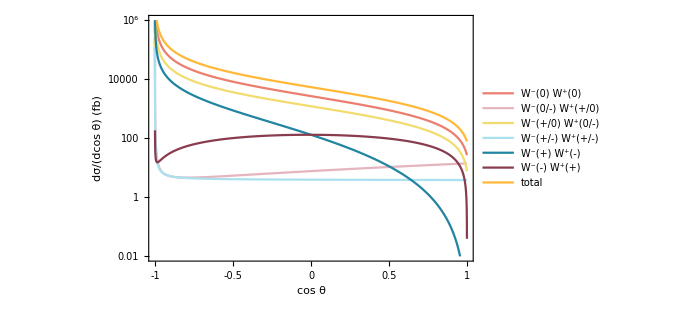

```mathematica
lineplot1=ListLogPlot[{Transpose[{Cos[thetaList],factor*ww00}],Transpose[{Cos[thetaList],factor*ww01}],Transpose[{Cos[thetaList],factor*ww10}],Transpose[{Cos[thetaList],factor*ww11}],Transpose[{Cos[thetaList],factor*ww1m1}],Transpose[{Cos[thetaList],factor*wwm11}],Transpose[{Cos[thetaList],factor*(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][10],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["dσ/(dcos θ) (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["",Black,20],
PlotLegends->{Style[" W^-(0) W^+(0)",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{0.01,1000000}},FrameTicks->{{ticks1,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
(*Export["WWtt_angular_partonic.pdf",lineplot1]
```

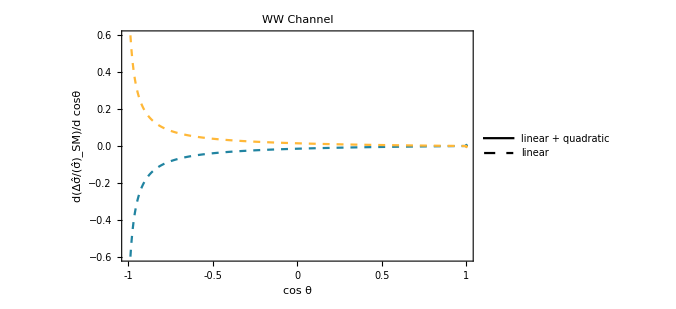

```mathematica
linearlineplot3=ListPlot[{Transpose[{-Cos[thetaList],(2 dytww11 + dytww00-2 ww11  - ww00)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}],Transpose[{-Cos[thetaList],(2 mdytww11 + mdytww00-2 ww11  - ww00)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)}]},Joined->True,PlotStyle->{Directive[ColorData[colorselecitonumber][6],Dashed],Directive[Dashed,ColorData[colorselecitonumber][2]]},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["cos θ",Black,17,FontFamily->"Times"],Style["d(Δσ̂/(σ̂)_SM)/d cosθ",Black,17,FontFamily->"Times"]},
PlotLabel->Style["WW Channel",Black,17],
PlotLegends->Placed[LineLegend[{Directive[Black],Directive[Black,Dashed]},{Style["linear + quadratic",FontFamily->"Times",15],Style["linear",FontFamily->"Times",15]}],{0.72,0.8}],
PlotRange->{{-1,1},{-0.6,0.6}},FrameTicks->{{Automatic,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,15],ImageSize->500]
```

```mathematica
(*Export["WWtt_angular_partonic_dyt2.pdf",lineplot3]
```

```mathematica
(*Export["WW_angular_1000_total.pdf",lineplot3]
```

```mathematica
dytww00
```

{-1.01162×10^-10,-1.00667×10^-10,-9.91812×10^-11,-9.6704×10^-11,-9.32337×10^-11,-8.87679×10^-11,-8.33038×10^-11,-7.68376×10^-11,-6.93653×10^-11,-6.08817×10^-11,-5.13813×10^-11,-4.08577×10^-11,-2.9304×10^-11,-1.67124×10^-11,-3.0745×10^-12,1.1619×10^-11,2.73779×10^-11,4.42129×10^-11,6.21356×10^-11,8.11582×10^-11,1.01294×10^-10,1.22556×10^-10,1.4496×10^-10,1.68522×10^-10,1.93257×10^-10,2.19184×10^-10,2.4632×10^-10,2.74686×10^-10,3.04301×10^-10,3.35188×10^-10,3.67368×10^-10,4.00866×10^-10,4.35705×10^-10,4.71914×10^-10,5.09517×10^-10,5.48545×10^-10,5.89026×10^-10,6.30993×10^-10,6.74478×10^-10,7.19514×10^-10,7.66138×10^-10,8.14387×10^-10,8.643×10^-10,9.15918×10^-10,9.69282×10^-10,1.02444×10^-9,1.08143×10^-9,1.14031×10^-9,1.20113×10^-9,1.26393×10^-9,1.32878×10^-9,1.39573×10^-9,1.46484×10^-9,1.53618×10^-9,1.6098×10^-9,1.68578×10^-9,1.76419×10^-9,1.8451×10^-9,1.92859×10^-9,2.01475×10^-9,2.10365×10^-9,2.19538×10^-9,2.29004×10^-9,2.38772×10^-9,2.48853×10^-9,2.59257×10^-9,2.69995×10^-9,2.81078×10^-9,2.92519×10^-9,3.04331×10^-9,3.16526×10^-9,3.29119×10^-9,3.42123×10^-9,3.55556×10^-9,3.69431×10^-9,3.83767×10^-9,3.9858×10^-9,4.13889×10^-9,4.29714×10^-9,4.46075×10^-9,4.62993×10^-9,4.80491×10^-9,4.98593×10^-9,5.17323×10^-9,5.36707×10^-9,5.56774×10^-9,5.77552×10^-9,5.99072×10^-9,6.21366×10^-9,6.44469×10^-9,6.68416×10^-9,6.93246×10^-9,7.18998×10^-9,7.45716×10^-9,7.73444×10^-9,8.02231×10^-9,8.32126×10^-9,8.63184×10^-9,8.95462×10^-9,9.29019×10^-9,9.6392×10^-9,1.00023×10^-8,1.03803×10^-8,1.07739×10^-8,1.1184×10^-8,1.16114×10^-8,1.20571×10^-8,1.25221×10^-8,1.30074×10^-8,1.35142×10^-8,1.40438×10^-8,1.45975×10^-8,1.51766×10^-8,1.57828×10^-8,1.64176×10^-8,1.70829×10^-8,1.77805×10^-8,1.85126×10^-8,1.92813×10^-8,2.0089×10^-8,2.09385×10^-8,2.18325×10^-8,2.27741×10^-8,2.37667×10^-8,2.48139×10^-8,2.59198×10^-8,2.70887×10^-8,2.83254×10^-8,2.96352×10^-8,3.10238×10^-8,3.24976×10^-8,3.40636×10^-8,3.57295×10^-8,3.75039×10^-8,3.93964×10^-8,4.14175×10^-8,4.35791×10^-8,4.58942×10^-8,4.83777×10^-8,5.10462×10^-8,5.39183×10^-8,5.70152×10^-8,6.03608×10^-8,6.39823×10^-8,6.79107×10^-8,7.21815×10^-8,7.68354×10^-8,8.19197×10^-8,8.74886×10^-8,9.36057×10^-8,1.00345×10^-7,1.07794×10^-7,1.16055×10^-7,1.25251×10^-7,1.35527×10^-7,1.4706×10^-7,1.60062×10^-7,1.74795×10^-7,1.91578×10^-7,2.1081×10^-7,2.3299×10^-7,2.58753×10^-7,2.88914×10^-7,3.2453×10^-7,3.67×10^-7,4.18199×10^-7,4.80688×10^-7,5.58041×10^-7,6.55361×10^-7,7.80142×10^-7,9.43735×10^-7,1.164×10^-6,1.47033×10^-6,1.9138×10^-6,2.58938×10^-6,3.68961×10^-6,5.65102×10^-6,9.62109×10^-6,0.0000192095,0.0000445341,1.0182×10^-6,0.0000445341}

```mathematica
(2 dytww11 + dytww00-2 ww11  - ww00)/(2 ww11 + wwm11 +  ww1m1 + 2 ww10  + 2 ww01 + ww00)
```

{-0.847009,-0.842546,-0.829437,-0.808471,-0.780835,-0.747958,-0.711345,-0.672435,-0.632506,-0.592613,-0.553578,-0.515997,-0.480272,-0.446644,-0.415228,-0.386046,-0.359054,-0.334164,-0.311261,-0.290217,-0.270893,-0.253155,-0.23687,-0.221913,-0.208167,-0.195522,-0.183879,-0.173147,-0.163243,-0.154091,-0.145624,-0.137779,-0.130502,-0.123743,-0.117455,-0.1116,-0.106139,-0.101039,-0.0962715,-0.0918082,-0.0876247,-0.0836988,-0.0800103,-0.0765408,-0.0732737,-0.0701937,-0.067287,-0.064541,-0.0619442,-0.0594859,-0.0571565,-0.0549471,-0.0528497,-0.0508567,-0.0489613,-0.047157,-0.0454382,-0.0437994,-0.0422357,-0.0407423,-0.0393152,-0.0379503,-0.036644,-0.035393,-0.0341939,-0.033044,-0.0319405,-0.0308809,-0.0298627,-0.0288838,-0.0279422,-0.0270358,-0.026163,-0.0253219,-0.0245112,-0.0237291,-0.0229745,-0.0222459,-0.0215422,-0.0208621,-0.0202048,-0.019569,-0.0189539,-0.0183586,-0.0177822,-0.0172239,-0.016683,-0.0161587,-0.0156504,-0.0151575,-0.0146793,-0.0142153,-0.013765,-0.0133278,-0.0129032,-0.0124908,-0.0120902,-0.011701,-0.0113227,-0.010955,-0.0105975,-0.0102499,-0.00991188,-0.00958313,-0.00926336,-0.00895229,-0.00864965,-0.0083552,-0.00806868,-0.00778988,-0.00751856,-0.00725453,-0.00699757,-0.0067475,-0.00650412,-0.00626726,-0.00603676,-0.00581244,-0.00559415,-0.00538174,-0.00517506,-0.00497398,-0.00477836,-0.00458807,-0.00440299,-0.004223,-0.00404798,-0.00387782,-0.00371242,-0.00355167,-0.00339547,-0.00324373,-0.00309635,-0.00295325,-0.00281433,-0.00267952,-0.00254874,-0.0024219,-0.00229893,-0.00217977,-0.00206433,-0.00195255,-0.00184437,-0.00173973,-0.00163856,-0.0015408,-0.0014464,-0.0013553,-0.00126746,-0.00118282,-0.00110133,-0.00102294,-0.000947618,-0.000875312,-0.000805982,-0.00073959,-0.000676096,-0.000615464,-0.00055766,-0.000502651,-0.000450406,-0.000400894,-0.000354086,-0.000309957,-0.00026848,-0.000229631,-0.000193388,-0.000159729,-0.000128633,-0.000100082,-0.0000740547,-0.0000505334,-0.0000294968,-0.0000109198,5.23293×10^-6,0.0000190225,0.0000305811,0.000040278,0.0000495875,0.000070393,0.00617073,0.000070393}

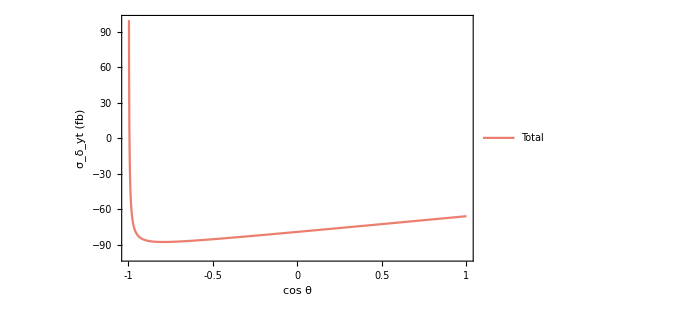

```mathematica
lineplot4=ListPlot[{Transpose[{Cos[thetaList],factor*(2 dytww11 + dytww00-2 ww11  - ww00)}]},Joined->True,PlotStyle->{ColorData[colorselecitonumber][1],ColorData[colorselecitonumber][2],ColorData[colorselecitonumber][3],ColorData[colorselecitonumber][4],ColorData[colorselecitonumber][6],
ColorData[colorselecitonumber][9],ColorData[colorselecitonumber][2],{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed},{Black,Dashed}},Frame->True,BaseStyle->{FontFamily->"Times"},FrameLabel->{Style["cos θ",Black,22,FontFamily->"Times"],Style["σ_δ_yt (fb)",Black,22,FontFamily->"Times"]},
PlotLabel->Style["",Black,20],
PlotLegends->{Style[" Total",Black,18,FontFamily->"Times"],Style[" W^-(0/-) W^+(+/0)",Black,18,FontFamily->"Times"],Style[" W^-(+/0) W^+(0/-)",Black,18,FontFamily->"Times"],Style[" W^-(+/-) W^+(+/-)",Black,18,FontFamily->"Times"],Style[" W^-(+) W^+(-)",Black,18,FontFamily->"Times"],Style[" W^-(-) W^+(+)",Black,18,FontFamily->"Times"],Style[" total",Black,18,FontFamily->"Times"]},
PlotRange->{{-1,1},{-100,100}},FrameTicks->{{Automatic,Automatic},{{-1,-0.5,0,0.5,1},Automatic}},
FrameTicksStyle->Directive[Black,16],ImageSize->500]
```

```mathematica
factor*(2 dytww11 + dytww00-2 ww11  - ww00)
```

{-65.9709,-65.973,-65.9791,-65.9894,-66.0037,-66.0221,-66.0445,-66.0711,-66.1016,-66.1363,-66.175,-66.2177,-66.2644,-66.3151,-66.3698,-66.4285,-66.4911,-66.5576,-66.6281,-66.7024,-66.7806,-66.8626,-66.9485,-67.0381,-67.1315,-67.2286,-67.3294,-67.4338,-67.5419,-67.6536,-67.7688,-67.8876,-68.0099,-68.1356,-68.2647,-68.3972,-68.533,-68.672,-68.8143,-68.9599,-69.1085,-69.2603,-69.4151,-69.5729,-69.7336,-69.8973,-70.0638,-70.233,-70.4051,-70.5798,-70.7571,-70.937,-71.1194,-71.3043,-71.4916,-71.6812,-71.873,-72.0671,-72.2633,-72.4616,-72.6619,-72.8642,-73.0683,-73.2743,-73.482,-73.6914,-73.9024,-74.1149,-74.3289,-74.5443,-74.7611,-74.9791,-75.1982,-75.4185,-75.6398,-75.862,-76.0852,-76.3091,-76.5337,-76.759,-76.9849,-77.2112,-77.438,-77.6651,-77.8924,-78.1198,-78.3474,-78.5749,-78.8024,-79.0296,-79.2566,-79.4833,-79.7095,-79.9352,-80.1602,-80.3846,-80.6081,-80.8308,-81.0525,-81.2731,-81.4925,-81.7106,-81.9273,-82.1426,-82.3563,-82.5683,-82.7785,-82.9868,-83.1931,-83.3973,-83.5992,-83.7988,-83.9958,-84.1903,-84.382,-84.5708,-84.7566,-84.9392,-85.1185,-85.2943,-85.4664,-85.6347,-85.7991,-85.9592,-86.1149,-86.2659,-86.4121,-86.5532,-86.689,-86.819,-86.9431,-87.0609,-87.172,-87.2761,-87.3727,-87.4613,-87.5415,-87.6126,-87.674,-87.725,-87.7649,-87.7927,-87.8074,-87.808,-87.7931,-87.7614,-87.711,-87.6403,-87.5468,-87.4282,-87.2813,-87.1028,-86.8885,-86.6336,-86.3321,-85.9771,-85.5601,-85.0708,-84.4963,-83.8208,-83.0245,-82.082,-80.961,-79.6193,-78.0012,-76.0317,-73.6087,-70.5891,-66.7685,-61.8459,-55.3642,-46.6012,-34.363,-16.5594,10.7376,55.6217,136.965,307.16,755.188,2488.02,7992.4,2488.02}